```mathematica
n=8;
```

```mathematica
f[i_,x_]:=Sum[c[i,j]x^(j-1),{j,n}];a=Table[D[f[i,x],{x,k-1}],{k,n/2}]
```

{c[i,1]+x c[i,2]+x^2 c[i,3]+x^3 c[i,4]+x^4 c[i,5]+x^5 c[i,6]+x^6 c[i,7]+x^7 c[i,8],c[i,2]+2 x c[i,3]+3 x^2 c[i,4]+4 x^3 c[i,5]+5 x^4 c[i,6]+6 x^5 c[i,7]+7 x^6 c[i,8],2 c[i,3]+6 x c[i,4]+12 x^2 c[i,5]+20 x^3 c[i,6]+30 x^4 c[i,7]+42 x^5 c[i,8],6 c[i,4]+24 x c[i,5]+60 x^2 c[i,6]+120 x^3 c[i,7]+210 x^4 c[i,8]}

```mathematica
df[j_,b_]:=a/.x->b/.i->j
```

```mathematica
r=Solve[Flatten[Join[Table[df[i,0][[k]]==HeavisideTheta[0.1+n/2-i](KroneckerDelta[i,k]+KroneckerDelta[i,k+n/2]),{k,1,n/2},{i,n}],Table[df[i,1][[k]]==HeavisideTheta[-0.1+i-n/2](KroneckerDelta[i,k]+KroneckerDelta[i,k+n/2]),{k,1,n/2},{i,n}]]],Flatten[Table[c[i,j],{i,n},{j,n}]]][[1]];
```

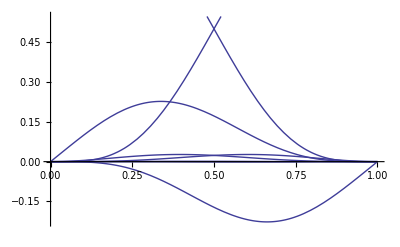

```mathematica
Plot[Table[f[i,x],{i,n}]/.r,{x,0,1}]
```

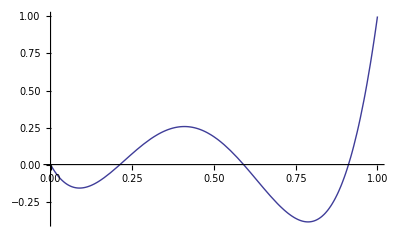

```mathematica
Plot[df[8,x][[4]]/.r,{x,0,1}]
```

```mathematica
df[1,x][[1]]
```

c[i,1]+x c[i,2]+x^2 c[i,3]+x^3 c[i,4]+x^4 c[i,5]+x^5 c[i,6]